```mathematica
dx = 400;
```

```mathematica
σ1=0.5; σ2 = 0.5; σ3=0.9;
μ1 = 0 +dx; μ2 = -0.4 + dx; μ3 = -0.4 + dx;
a = 0.90; b = 1.62;
```

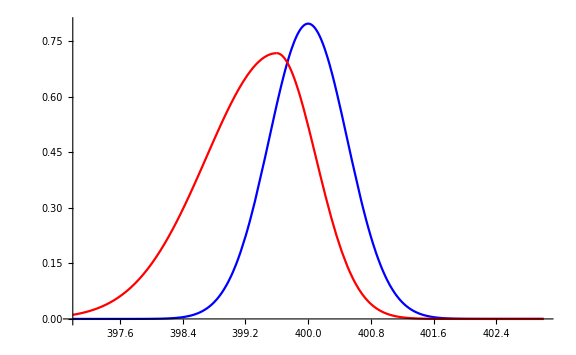

```mathematica
plot1 = Plot[1.0 / (σ1 * Sqrt[2 * Pi]) * Exp[-1.0/2.0 * ((x - μ1) / σ1)^2],{x,-3+dx,3+dx}, Axes->{True,False}, ImageSize->Large, PlotStyle-> Blue,PlotRange -> All];
plot2 = Plot[a * 1.0 / (σ2 * Sqrt[2 * Pi]) * Exp[-1.0/2.0 * ((x - μ2) / σ2)^2],{x,-0.4+dx,3+dx}, Axes->{True,True}, ImageSize->Large, PlotRange -> All, PlotStyle->Red];
plot3 = Plot[b * 1.0 / (σ3 * Sqrt[2 * Pi]) * Exp[-1.0/2.0 * ((x - μ3) / σ3)^2],{x,-3+dx,-0.4+dx}, Axes->{True,True}, ImageSize->Large, PlotRange -> All, PlotStyle->Red, Epilog-> Graphics[Inset[x^2+y^2==1,{400,10}]]];
Show[plot1,plot2,plot3, PlotRange -> All, PlotLegends->Automatic]
```